```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
χ=x[[15]];
Growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
Starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
InvaderStarvation =  N[ts*-Bm/(Em*(Log[1-f0*M^(γ-1)] + Log[M/(M*(1+χ))]))]*(1+RandomReal[{-noise,noise}]);
Mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
InvaderRecovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(1+χ)*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
Maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
InvaderMaintenance = (ts*ef*B0*(M*(1+χ))^η)*(1+RandomReal[{-noise,noise}]);
Resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance}
);
```

```mathematica
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =M,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.00001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
GrowthOverM=RF[[1]];
StarvationOverM=RF[[2]];
```

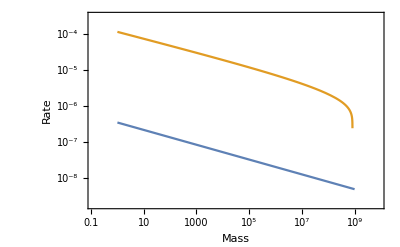

```mathematica
GrowthVStarvationPlot=LogLogPlot[{Re[GrowthOverM],StarvationOverM},{M,1,10^9},Frame->True,FrameLabel->{"Mass","Rate"}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_GvS.pdf",GrowthVStarvationPlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_GvS.pdf

```mathematica
Mvalues=N[RecurrenceTable[{B[n+1] == B[n]+1/50B[n],B[1]==1},B,{n,1,1500}]];
```

```mathematica
GvSNoise=Table[
parameters={
(*noise*)0.5,
(*ts*)1,
(*M*)Mass =M,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.00001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
{M,Growth,Starvation},
{M,Mvalues}];
```

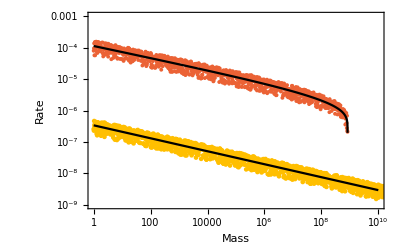

```mathematica
GrowthVStarvationPlot=Show[{
ListLogLogPlot[Transpose[{GvSNoise[[All,1]],GvSNoise[[All,2]]}],PlotRange->{{1,10^10},{10^(-9),10^(-3)}},Frame->True,PlotStyle->ColorData[97,8],FrameLabel->{"Mass","Rate"}],
ListLogLogPlot[Transpose[{GvSNoise[[All,1]],GvSNoise[[All,3]]}],PlotStyle->ColorData[97,4]],
LogLogPlot[GrowthOverM,{M,1,10^10},PlotStyle->Black,PlotRange->All],
LogLogPlot[StarvationOverM,{M,1,10^10},PlotStyle->Black,PlotRange->All]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_GvS.pdf",GrowthVStarvationPlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_GvS.pdf